```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
file=Import["V12.pfl","Table"];
nUp=file[[3,1]];
nDn=file[[4,1]];
ptUp=file[[6;;6+nUp]];
ptDn=file[[6+nUp+2;;6+nUp+2+nDn]];
```

```mathematica
Pts=Reverse[ptUp]~Join~ptDn[[2;;-2]];
```

```mathematica
n=Length[Pts]
```

400

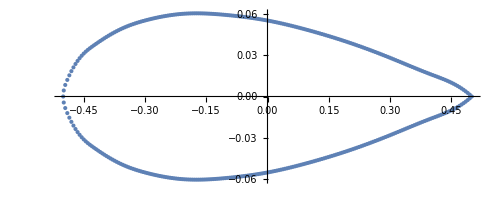

```mathematica
ListPlot[Pts,AspectRatio->Automatic]
```

```mathematica
Export["V12wing"<>ToString[n],
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.9    |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2020/07/22     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2020 Ilia Marchevsky, Kseniia Kuzmina, Evgeniya Ryatina  |
*-----------------------------------------------------------------------------*
| File name: circle"<>ToString[n]<>StringRepeat[" ",59-StringLength@ToString[n]]<>"|
| Info: Circular airfoil ("<>ToString[n]<>" panels)"<>StringRepeat[" ",44-StringLength@ToString[n]]<>"|
\\*---------------------------------------------------------------------------*/
"}~Join~{"r = {"}~Join~((ToString[SetPrecision[#,17]]<>",")&/@(Pts[[1;;-2]]))~Join~((ToString[SetPrecision[#,17]])&/@(Pts[[{-1}]]))~Join~{" };"},"Table"]
```

V12wing400